# Beam PixeLink

## Last Updated: 07/18/2023

```mathematica
(*Quit[];*)
```

```mathematica
(*todo: implement folders and autosearch without SetDirectory*)
(*todo: implement image rotation via thresholding*)
```

## File Location & Name

```mathematica
(*set directory and filetype*)
SetDirectory["/Users/EGGS1/Pictures/2024_01_08_729nm_alignment"];
imgName="2231PM.bmp";
```

# Prep

## Plotting Setup

```mathematica
SetOptions[Plot,ImageSize->Large,PlotRange->Full];
SetOptions[ListPlot,ImageSize->Large,PlotRange->Full];
```

```mathematica
Off[General::munfl];
```

## Global Variables

```mathematica
(*units*)
inch=2.54*^-2;
cm=1*^-2;mm=1*^-3;um=1*^-6;nm=1*^-9;
```

```mathematica
(*length per pixel for pixelink camera*)
pixelWidth=4.4*^-6;
```

# Process

## Process Image

```mathematica
(*gaussian kernel, i.e. 2σ*)
nGauss=30;
(*range of pixels to take in*)
window={200,200};
```

## Import Image

```mathematica
(*import image and get dimensions*)
imgRaw=ImageData[ColorConvert[Import[imgName],"Grayscale"]];
imgRawDim=Dimensions[imgRaw]//Reverse;
imgRaw//Dimensions
```

{1200,1600}

```mathematica
(*apply gaussian filtering to smooth the pixels*)
imgGauss=GaussianFilter[imgRaw,nGauss];
```

## Crop and Center Image

```mathematica
(*center image at max fluorescence*)
centerGauss=Reverse[Position[imgGauss,Max[imgGauss]][[1]]];
```

```mathematica
(*get image window while staying within bounds*)
{x1,x2}=Clip[centerGauss[[1]]+{-window[[1]],window[[1]]},{1,imgRawDim[[1]]}];
{y1,y2}=Clip[centerGauss[[2]]+{-window[[2]],window[[2]]},{1,imgRawDim[[2]]}];
```

```mathematica
(*clip image and get new center*)
imgProcessed=imgRaw[[y1;;y2,x1;;x2]];
centerProcessed=Reverse[Position[imgProcessed,Max[imgProcessed]][[1]]];
```

```mathematica
(*integrate pixel count along y- and x- axis, respectively*)
{xVals,yVals}={Total[#],Total[#//Transpose]}&[imgProcessed];
(*only take a single x- and y- slice at the center*)
(*{xVals,yVals}={imdGauss[[center[[2]],;;]],imdGauss[[;;,center[[1]]]]};*)
```

## Fit Image

## Fit Setup

```mathematica
(*fit a gaussian profile*)
(*note: factor of 2 in exponent is b/c intensity is square of electric field*)
xFitEqn=a*Exp[-2((x-x0)/wx)^2]+b;
yFitEqn=a*Exp[-2((y-y0)/wy)^2]+b;
```

```mathematica
(*fitting constraints; note - adding constraints may hurt fitting*)
xFitConstr={};
yFitConstr={};
```

```mathematica
(*fitting parameters*)
xFitVars={{x0,centerProcessed[[1]]},{wx,150},{a,Max[xVals]},{b,Min[xVals]}}
yFitVars={{y0,centerProcessed[[2]]},{wy,300},{a,Max[yVals]},{b,Min[yVals]}}
```

{{x0,201},{wx,150},{a,28.7765},{b,2.80392}}

{{y0,194},{wy,300},{a,27.9451},{b,2.7451}}

## Fitting

```mathematica
(*fit!*)
xFit=NonlinearModelFit[xVals,Join[{xFitEqn},xFitConstr],xFitVars,x,MaxIterations->1*^6];
yFit=NonlinearModelFit[yVals,Join[{yFitEqn},yFitConstr],yFitVars,y,MaxIterations->1*^6];
```

```mathematica
{xFitParams,yFitParams}={xFit["ParameterTable"],yFit["ParameterTable"]}
```

{ | Estimate | Standard Error | t-Statistic | P-Value
x0 | 199.384 | 0.264131 | 754.867 | 0.
wx | -37.7139 | 0.556845 | -67.7278 | 3.23471×10^-220
a | 23.7243 | 0.29307 | 80.9509 | 6.92268×10^-249
b | 3.55925 | 0.0783358 | 45.4358 | 2.23899×10^-159, | Estimate | Standard Error | t-Statistic | P-Value
y0 | 205.067 | 0.182606 | 1123. | 0.
wy | 47.0508 | 0.391838 | 120.077 | 3.80942×10^-314
a | 23.2505 | 0.160182 | 145.151 | 0.
b | 2.9366 | 0.04961 | 59.1937 | 4.35696×10^-199}

```mathematica
(*extract values*)
{wxFit,wyFit}=pixelWidth*{xFitParams[[1,1,3,2]],yFitParams[[1,1,3,2]]};
{wxFitErr,wyFitErr}=pixelWidth*{xFitParams[[1,1,3,3]],yFitParams[[1,1,3,3]]};
```

# Display

## Prepare Figures

```mathematica
(*display beam waist values with error*)
waistDisplay=MatrixForm[{
"w_x="<>ToString[N[wxFit/um]]<>"±"<>ToString[Round[N[wxFitErr/um],0.1]]<>"μm",
"w_y="<>ToString[N[wyFit/um]]<>"±"<>ToString[Round[N[wyFitErr/um],0.1]]<>"μm"
}];
```

```mathematica
(*get max fluorescence at any point along image to check for clipping/saturation*)
maxPlot=ListPlot[
Max/@imgRaw,
PlotRange->{0,1},
PlotLabel->imgName,
ImageSize->Large
];
```

```mathematica
(*combine raw data and fits*)
dataPlot=Show[{
ListPlot[{xVals,yVals},ImageSize->Large],
(*Plot[{xFit[x],yFit[x]},{x,0,2 *window[[1]]+1}]*)
Plot[{xFit[x],yFit[x]},{x,0,1500}]},
ImageSize->Large,
PlotLabel->imgName
];
```

```mathematica
(*display processed image*)
imgDisplay=Image[imgProcessed,ImageSize->Small];
```

## Show

{-Graphics-,(w_x=-165.941±2.5μm
w_y=207.023±1.7μm)}

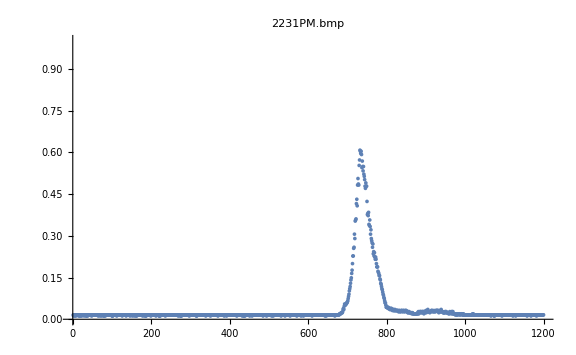
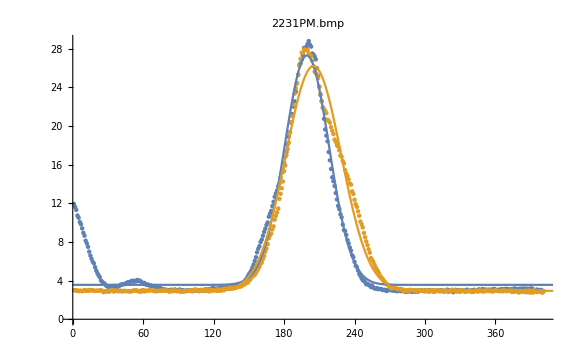

```mathematica
{imgDisplay,waistDisplay}
{maxPlot,dataPlot}
```

# Data Store

```mathematica
(*Image[imdRaw]*)
```

```mathematica
(*old way*)
```

```mathematica
(*no sum way*)
```

# Deprecated

```mathematica
(*bgrX=Mean[xVals[[;;100]]];bgrY=Mean[yVals[[;;100]]];
x2=xVals-bgrX;y2=yVals-bgrY;
maxX=Max[x2];maxY=Max[y2];
intX=Interpolation[xVals];intY=Interpolation[yVals];*)
```

```mathematica
(*center2={Position[x2,maxX][[1,1]],Position[y2,maxY][[1,1]]};*)
```

```mathematica
(*xRes=x/.(FindRoot[intX[x]==0.5maxX,{x,500}]);
yRes=y/.(FindRoot[intY[y]==0.5 maxY,{y,380}]);*)
```

```mathematica
(*Abs[{xRes,yRes}-center2]/(√(1/2 Log[2]))*pixelWidth/um*)
```